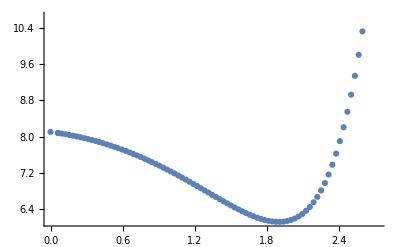

```mathematica
f={{0,8.104713},{0.062500,8.079927},{0.062500,8.079927},{0.093750,8.066607},{0.125000,8.052463},{0.156250,8.037415},{0.187500,8.021407},{0.218750,8.004400},{0.250000,7.986369},{0.281250,7.967292},{0.312500,7.947156},{0.343750,7.925949},{0.375000,7.903665},{0.406250,7.880298},{0.437500,7.855845},{0.468750,7.830303},{0.500000,7.803672},{0.531250,7.775953},{0.562500,7.747146},{0.593750,7.717254},{0.625000,7.686281},{0.656250,7.654233},{0.687500,7.621116},{0.718750,7.586937},{0.750000,7.551707},{0.781250,7.515438},{0.812500,7.478144},{0.843750,7.439842},{0.875000,7.400552},{0.906250,7.360298},{0.937500,7.319106},{0.968750,7.277008},{1.000000,7.234041},{1.031250,7.190247},{1.062500,7.145674},{1.093750,7.100377},{1.125000,7.054417},{1.156250,7.007864},{1.187500,6.960796},{1.218750,6.913302},{1.250000,6.865479},{1.281250,6.817436},{1.312500,6.769294},{1.343750,6.721186},{1.375000,6.673259},{1.406250,6.625676},{1.437500,6.578613},{1.468750,6.532266},{1.500000,6.486850},{1.531250,6.442597},{1.562500,6.399765},{1.593750,6.358634},{1.625000,6.319509},{1.656250,6.282726},{1.687500,6.248652},{1.718750,6.217685},{1.750000,6.190265},{1.781250,6.166870},{1.812500,6.148025},{1.843750,6.134304},{1.875000,6.126336},{1.906250,6.124813},{1.937500,6.130493},{1.968750,6.144209},{2.000000,6.166879},{2.031250,6.199510},{2.062500,6.243217},{2.093750,6.299223},{2.125000,6.368880},{2.156250,6.453678},{2.187500,6.555255},{2.218750,6.675404},{2.250000,6.816078},{2.281250,6.979371},{2.312500,7.167474},{2.343750,7.382572},{2.375000,7.626666},{2.406250,7.901335},{2.437500,8.207753},{2.468750,8.547417},{2.500000,8.923138},{2.531250,9.339242},{2.562500,9.801469},{2.593750,10.316864},{2.625000,10.892747},{2.656250,11.532512},{2.687500,12.222618},{2.718750,12.900751}};
ListPlot[f]
```

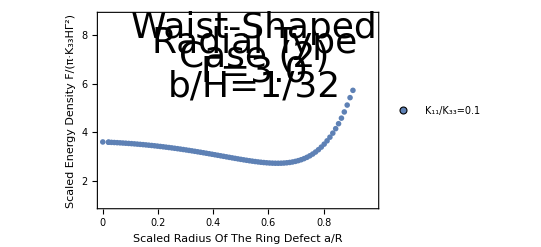

```mathematica
ee=f*Table[{1/3,4/9},{i,0,87}];
ListPlot[{ee},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{2,4,6,8},None},{{0,0.2, 0.4, 0.6, 0.8},None}}, PlotRange->{{0,0.98},{1,8.8}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=0.1","K_11/K_33=2.0","K_11/K_33=3.0","K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Waist-Shaped",Directive[Black,36]],{0.55,8.3}],Text[Style["Radial Type",Directive[Black,36]],{0.55,7.7}],Text[Style["Case (2)",Directive[Black,36]],{0.55,7.1}],Text[Style["Γ=3.0",Directive[Black,36]],{0.55,6.5}],Text[Style["b/H=1/32",Directive[Black,36]],{0.55,5.9}]}]
```